日期和时间

在 Wolfram 语言中，Now 将给出你当前的日期和时间。

获取当前的日期和时间(截至我写这篇文章的时候)：

```mathematica
Now
```

Fri 17 Mar 2017 13:39:00GMT-5.

你可以在此基础上进行计算，例如增加一个星期。

在当前日期和时间上增加一个星期：

```mathematica
Now+LinguisticAssistant
```

Fri 24 Mar 2017 13:39:00GMT-5.

使用 ctrl= 来输入任何标准格式的日期。

输入一个日期：

```mathematica
LinguisticAssistant
```

Day: Thu 23 Jun 1988

你可以对日期进行算术运算，比如说，用减法来计算它们之间的差值。

将两个日期进行相减：

```mathematica
Now-LinguisticAssistant
```

10494. days

将日期差值转换为年：

```mathematica
UnitConvert[Now-LinguisticAssistant,"Years"]
```

28.7507 yr

DayRange 是 Range 在日期方面的相似函数。

给出从昨天到明天的日期列表：

```mathematica
DayRange[Yesterday,Tomorrow]
```

{Day: Thu 16 Mar 2017,Day: Fri 17 Mar 2017,Day: Sat 18 Mar 2017}

DayName 用于计算某个特定日期是星期几。

计算从现在开始的 45 天后是星期几：

```mathematica
DayName[Today+LinguisticAssistant]
```

Monday

一旦你知道了一个日期，你可以计算很多东西。例如，MoonPhase 将给出月相(或者更准确地说，从地球上看月球时被照亮的部分)。

计算现在的月相：

```mathematica
MoonPhase[Now]
```

0.7606

计算某一日期的月相：

```mathematica
MoonPhase[LinguisticAssistant]
```

0.5756

生成一个月相的图标：

```mathematica
MoonPhase[LinguisticAssistant,"Icon"]
```

-Graphics-

如果你知道日期和地球上的某个位置，你就可以算出太阳何时升起和落下。

计算今天在我当前位置的日落时间：

```mathematica
Sunset[Here,Today]
```

Minute: Fri 17 Mar 2017 19:04GMT-5.

计算连续的两次日出之间的时间：

```mathematica
Sunrise[Here,Tomorrow]-Sunrise[Here,Today]
```

1438 min

它们离一整天(24小时)还差 2 分钟：

```mathematica
Sunrise[Here,Tomorrow]-Sunrise[Here,Today]-LinguisticAssistant
```

-2 min

时区是许多微妙的因素之一。LocalTime 将给出特定地点的时区的时间。

查找纽约市的本地时间：

```mathematica
LocalTime[LinguisticAssistant]
```

Fri 17 Mar 2017 14:44:22GMT-4.

查找伦敦的本地时间：

```mathematica
LocalTime[LinguisticAssistant]
```

Fri 17 Mar 2017 18:44:29GMT

在 Wolfram 语言中拥有大量数据的众多领域中，天气是其中之一。函数 AirTemperatureData 使用这些数据来给出某一特定时间和地点的历史气温。

找出昨天下午 6 点当前位置的气温：

```mathematica
AirTemperatureData[Here,LinguisticAssistant]
```

39.92 °F

如果你提供了一对日期，AirTemperatureData 会计算出这些日期之间的估计温度的时间序列。

给出从一周前到现在的气温时间序列：

```mathematica
AirTemperatureData[Here,{LinguisticAssistant,Now}]
```

TimeSeries[…]

DateListPlot 是 ListPlot 在时间序列方面的相似函数，其中每个值都发生在一个特定的日期。

绘制气温列表：

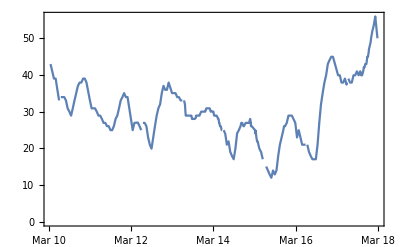

```mathematica
DateListPlot[AirTemperatureData[Here,{LinguisticAssistant,Now}]]
```

该图显示—毫不奇怪—白天的温度比晚上高。

作为另一个例子，让我们看一下更久远的数据。WordFrequencyData 告诉我们一个特定的词出现的频率，比如说在某年出版的书的样本中。通过观察这些年和几个世纪以来的变化，我们可以看到很多历史。

找出“automobile”一词的出现频率的时间序列：

```mathematica
WordFrequencyData["automobile","TimeSeries"]
```

TimeSeries[…]

汽车在 1900 年左右开始存在，但现在已经逐渐不再称它为“automobiles”：

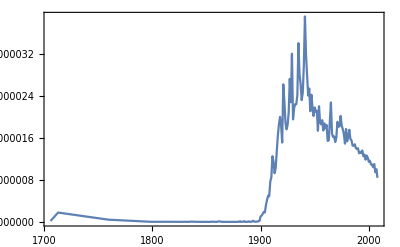

```mathematica
DateListPlot[WordFrequencyData["automobile","TimeSeries"]]
```

WordFrequencyData 是为了方便比较不同词语的出现频率。让我们看看“君主制”和“民主制”这些年来的表现如何。“民主”现在肯定更受欢迎，但“君主制”在 1700 年代和 1800 年代更受欢迎。

比较“君主制”和“民主制”的历史词频：

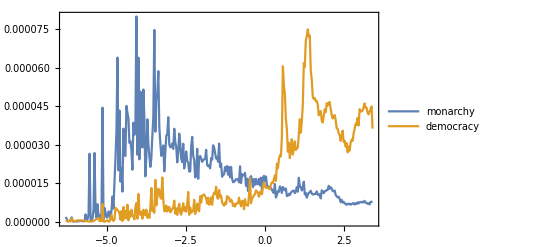

```mathematica
DateListPlot[WordFrequencyData[{"monarchy","democracy"},"TimeSeries"]]
```

词汇

Now |   | 当前日期和时间
Today |   | 表示今天的日期对象
Tomorrow |   | 表示明天的日期对象
Yesterday |   | 表示昨天的日期对象
DayRange[date_1,date_2] |   | 从 date_1 到 date_2 的日期列表
DayName[date] |   | 给定日期是星期几
MoonPhase[date] |   | 给定日期的月相
Sunrise[location,date] |   | 给定日期和位置的日出时间
Sunset[location,date] |   | 给定日期和位置的日落时间
LocalTime[location] |   | 给定位置的当地时间
AirTemperatureData[location,time] |   | 给定时间和位置的气温
AirTemperatureData[location,{time_1,time_2}] |   | 给定位置处从 time_1 到 time_2 的气温时间序列
DateListPlot[timeseries] |   | 绘制时间序列
WordFrequencyData["word","TimeSeries"] |   | 词频时间序列

"共有 13 道习题"
"以及 7 道附加题" | "开始练习 »"

计算自 1900 年 1 月 1 日以来已经过去了多少天。»

| 期望输出示例： |  
  | 42809. "days" |

计算 2000 年 1 月 1 日是星期几。»

| 期望输出示例： |  
  | Saturday |

找到十万天前的日期。»

| 期望输出示例： |  
  | "Sun 2 Jun 1743 14:40:00""GMT"-5. |

查找德里(Delhi)的当地时间。»

| 期望输出示例： |  
  | "Fri 17 Mar 2017 01:15:29""GMT+"5.5 |

用今天的日出减去今天的日落，求出今天的日照时间长度。»

| 期望输出示例： |  
  | -717 "min" |

生成当前月相的图标。»

| 期望输出示例： |  
  |  |

创建未来 10 天内的月相值的列表。»

| 期望输出示例： |  
  | {0.6748,0.5837,0.489,0.3932,0.2994,0.2112,0.1326,0.06838,0.02335,0.001956} |

生成一个从今天到 10 天后的月相的图标列表。»

| 期望输出示例： |  
  | {,,,,,,,,,} |

计算今天纽约市的日出和伦敦的日出之间的时间差值。»

| 期望输出示例： |  
  | 294 "min" |

求出昨天中午埃菲尔铁塔的气温。»

| 期望输出示例： |  
  | 64.94 "°F" |

绘制过去一周埃菲尔铁塔的温度。»

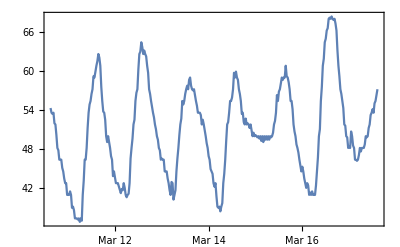
| 期望输出示例： |  
  | -Graphics- |

求出洛杉矶和纽约市之间现在的气温差值。»

| 期望输出示例： |  
  | 19.08 "°F" |

绘制 “groovy” 一词的历史频率。»

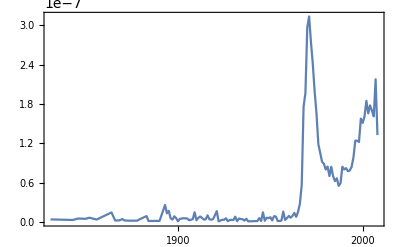
| 期望输出： |  
  | -Graphics- |

计算自 1900 年 1 月 1 日以来已经过去了多少个星期。»

| 期望输出： |  
  | 6115.57 "wk" |

计算今天下午 3 点到今天日落之间的时间。»

| 期望输出： |  
  | 4. "h" |

生成一个 1959 年 8 月 29 日的月相图标。»

| 期望输出： |  
  |  |

将未来 30 天内的月相值绘制为线条图。»

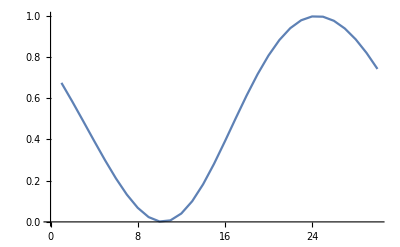
| 期望输出： |  
  | -Graphics- |

创建一个操作界面，控制未来 15 天内的月相图标。»

| 期望输出： |  
  |  |

在一列中显示从今天开始的 10 天内的日出时间。»

| 期望输出： |  
  | "Minute: ""Sat 18 Mar 2017 07:00""GMT"-5.
"Minute: ""Sun 19 Mar 2017 06:59""GMT"-5.
"Minute: ""Mon 20 Mar 2017 06:57""GMT"-5.
"Minute: ""Tue 21 Mar 2017 06:56""GMT"-5.
"Minute: ""Wed 22 Mar 2017 06:54""GMT"-5.
"Minute: ""Thu 23 Mar 2017 06:52""GMT"-5.
"Minute: ""Fri 24 Mar 2017 06:51""GMT"-5.
"Minute: ""Sat 25 Mar 2017 06:49""GMT"-5.
"Minute: ""Sun 26 Mar 2017 06:47""GMT"-5.
"Minute: ""Mon 27 Mar 2017 06:46""GMT"-5. |

将 “science” 和 “technology” 这两个词的历史频率绘制在一张图中。»

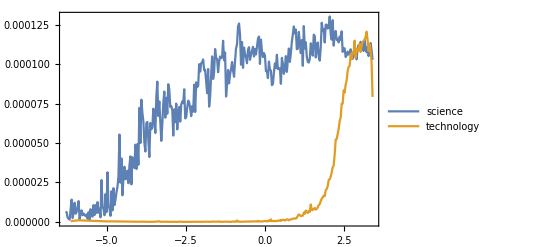
| 期望输出： |  
  | -Graphics- |

问&答

我怎样才能获得一个字符串形式的日期？

使用 DateString[date]。对于字符串的格式有很多选择。例如，DateString[date,"DateShort"] 将使用短日期和月份名称。

我如何从一个日期中提取月份或其他元素？

使用 DateValue。DateValue[date,"Month"] 将给出月份编号，DateValue[date,"MonthName"] 将给出月份名称，等等。

在 Wolfram 语言中，日期可以是过去多远的时间？

你想多远就多远。Wolfram 语言知道历史上的日历系统，以及时区的历史。它还拥有准确计算日出的数据，等等，至少可以追溯到 1000 年前。

为什么日出和日落只精确到分钟？

因为你无法在不知道空气温度等影响地球大气层中光线弯曲的因素的情况下更准确地计算出太阳实际升起和落下的时间。

Wolfram 语言从哪里获得空气温度数据？

位于机场和其他地方的全世界的气象站网络。如果你有自己的气温测量设备，你可以通过 Wolfram Data Drop(参见第 43 节)把它连接到 Wolfram 语言。

什么是时间序列？

这是一种指定某个事物在一系列时间内的值的方法。您可以在 Wolfram 语言中以 TimeSeries[{{time_1,value_1},{time_2,value_2},...}] 的形式来输入时间序列。Wolfram 语言可以让你对时间序列进行算术运算和许多其他操作。

DateListPlot 是做什么的？

它针对时间或日期来绘制数值。这些值可以以 TimeSeries[...] 的形式给出，也可以以 {{time_1,value_1},{time_2,value_2},...} 形式的列表来给出。

技术笔记

Wolfram 语言会根据你所在的国家来决定是把 8/10/15 这样的日期解释为月/日/年还是日/月/年。如果需要，你可以选择另一种解释。

Monday 等是具有内在意义的符号，而不是字符串。

DateObject 允许你指定一个日期的“颗粒度”(日、周、月、年、十年等)。CurrentDate、NextDate、DateWithinQ 等都是对粒度类型日期的操作。

你可以使用 InputForm 来查看 DateObject[...] 的“内部”内容。

探索更多

Wolfram 语言中的日期和时间指南 »